```mathematica
f={λ,η,γ,α,δ,β}↦{t,R,C,S}↦{
α S-β C,
γ R-δ S C, 
η R S - λ S
}
```

Function[{λ,η,γ,α,δ,β},Function[{t,R,C,S},{α S-β C,γ R-δ S C,η R S-λ S}]]

```mathematica
rkf45=Module[{rkf45prime,β,α,c,cHat,cT},
β=N[{{2/9, 0, 0, 0, 0}, {1/12, 1/4, 0, 0, 0}, {69/128, -243/128, 135/64, 0, 0}, {-17/12, 27/4, -27/5, 16/15, 0}, {65/432, -5/16, 13/16, 4/27, 5/144}}];
α=Total/@β;
c={1/9,0,9/20,16/45,1/12,0};
cHat={47/450,0,12/25,32/225,1/30,6/25};
cT=cHat-c;
rkf45prime={f,tol}↦Apply[{t,x,h}↦Module[
{f0,f1,f2,f3,f4,f5,xNext,xHat,hNext,TE},
f0=f[t,x];
f1=f[t+α⟦1⟧h,x+h(β⟦1,1⟧ f0)];
f2=f[t+α⟦2⟧h,x+h(β⟦2,1⟧ f0+β⟦2,2⟧ f1)];
f3=f[t+α⟦3⟧h,x+h(β⟦3,1⟧ f0+β⟦3,2⟧ f1+β⟦3,3⟧ f2)];
f4=f[t+α⟦4⟧h,x+h(β⟦4,1⟧ f0+β⟦4,2⟧ f1+β⟦4,3⟧ f2+β⟦4,4⟧ f3)];
f5=f[t+α⟦5⟧h,x+h(β⟦5,1⟧ f0+β⟦5,2⟧ f1+β⟦5,3⟧ f2+β⟦5,4⟧ f3+β⟦5,5⟧ f3)];
xNext=x+h(c⟦1⟧f0+c⟦2⟧f1+c⟦3⟧f2+c⟦4⟧f3+c⟦5⟧f4);
xHat=x+h(cHat⟦1⟧f0+cHat⟦2⟧f1+cHat⟦3⟧f2+cHat⟦4⟧f3+cHat⟦5⟧f4+cHat⟦6⟧f5);
TE=h(cT⟦1⟧f0+cT⟦2⟧f1+cT⟦3⟧f2+cT⟦4⟧f3+cT⟦5⟧f4+cT⟦6⟧f5);
hNext=0.9 h(tol/Max[Abs[TE]])^(1/5);
If[
Max[Abs[TE]]>tol,
{t,x,hNext,True},
{t+h,xHat,hNext,False}
]
]];
{f,tol}↦Module[{
stepPrime=rkf45prime[{t,x}↦f[t,Sequence@@x],tol]
},
Apply[{t,x,h}↦Most@NestWhile[stepPrime,{t,x,h,True},#⟦4⟧&]]
]
];
```

```mathematica
initial={0,{0.1,0.1,0.1},0.01};
update=rkf45[f[0.01,0.04,0.02,0.1,0.03,0.05],10^-6];
update[initial]
```

{0.01,{0.10005,0.100017,0.099994},0.387092}

{{0,{0.1,0.1,0.1},0.01},{0.01,{0.10005,0.100017,0.099994},0.387092},{0.397092,{0.101974,0.100683,0.0997636},1.66961},{2.0667,{0.11002,0.103715,0.098809},2.9865},{5.0532,{0.123363,0.109756,0.0972493},3.74883},{8.80203,{0.13813,0.118338,0.0955285},4.08273},{12.8848,{0.151589,0.128754,0.0939059},4.2053},{17.0901,{0.162484,0.140403,0.0924529},4.24357},{21.3336,{0.170337,0.152837,0.0911546},4.25592},{25.5896,{0.174987,0.165716,0.0899666},4.26707},{29.8566,{0.176386,0.178762,0.0888369},4.28748},{34.1441,{0.174518,0.191728,0.0877125},4.32208},{38.4662,{0.169366,0.204377,0.0865409},4.37409},{42.8403,{0.16091,0.216474,0.0852696},4.44676},{47.287,{0.149107,0.227777,0.083845},4.54451},{51.8316,{0.133898,0.238024,0.0822114},4.64524},{56.4768,{0.115311,0.246876,0.0803218},4.54806},{61.0249,{0.0944203,0.253724,0.0782318},4.40091},{65.4258,{0.0719729,0.258453,0.0759704},4.25745},{69.6832,{0.0484752,0.26111,0.0735561},4.13276},{73.816,{0.0242956,0.261781,0.0710051},4.02872},{77.8447,{-0.000271409,0.260554,0.0683343},3.94364},{81.7883,{-0.0249718,0.257508,0.0655617},3.87535},{85.6637,{-0.0495758,0.252717,0.0627063},3.82222},{89.4859,{-0.0738696,0.246244,0.0597878},3.78325},{93.2692,{-0.0976501,0.238148,0.0568255},3.75808},{97.0272,{-0.120721,0.22848,0.0538382},3.74695},{100.774,{-0.14289,0.217284,0.0508432},3.75074},{104.525,{-0.163963,0.204595,0.0478563},3.77103},{108.296,{-0.183741,0.190436,0.0448915},3.81041},{112.106,{-0.202011,0.174817,0.0419603},3.87294},{115.979,{-0.21854,0.157732,0.0390714},3.96512},{119.944,{-0.233061,0.139142,0.0362302},4.09783},{124.042,{-0.24525,0.118968,0.0334373},4.19389},{128.236,{-0.25451,0.0975465,0.0307462},4.18153},{132.418,{-0.260298,0.0756735,0.0282431},4.14007},{136.558,{-0.262488,0.0537862,0.0259484},4.10134},{140.659,{-0.261089,0.0321555,0.0238576},4.07714},{144.736,{-0.256144,0.0109818,0.0219574},4.07185},{148.808,{-0.247692,-0.00955996,0.0202329},4.08767},{152.896,{-0.235758,-0.0292993,0.018669},4.12686},{157.023,{-0.220347,-0.0480594,0.0172516},4.19296},{161.216,{-0.20144,-0.0656487,0.0159676},4.15765},{165.373,{-0.179727,-0.081375,0.0148389},4.00787},{169.381,{-0.156301,-0.0947062,0.0138766},3.85232},{173.233,{-0.131788,-0.10566,0.0130588},3.72187},{176.955,{-0.106557,-0.114384,0.0123603},3.62054},{180.576,{-0.0808565,-0.121021,0.0117599},3.54509},{184.121,{-0.0548885,-0.125686,0.0112415},3.49139},{187.612,{-0.0288332,-0.128464,0.0107925},3.45608},{191.068,{-0.00286408,-0.129418,0.0104031},3.43687},{194.505,{0.0228466,-0.128594,0.0100654},3.43242},{197.938,{0.0481243,-0.126024,0.00977339},3.44222},{201.38,{0.0727899,-0.121734,0.00952172},3.46656},{204.846,{0.0966567,-0.115737,0.00930611},3.50654},{208.353,{0.119528,-0.108039,0.00912286},3.56431},{211.917,{0.141191,-0.0986358,0.00896876},3.6434},{215.561,{0.161412,-0.0875071,0.00884091},3.74966},{219.31,{0.179926,-0.0746122,0.00873661},3.89281},{223.203,{0.196419,-0.0598741,0.00865324},4.0473},{227.25,{0.21037,-0.0433327,0.0085886},4.05749},{231.308,{0.220869,-0.0257743,0.00854123},4.02376},{235.332,{0.227673,-0.00768371,0.00850636},3.98697},{239.319,{0.23077,0.0106178,0.00847864},3.96208},{243.281,{0.23021,0.0288869,0.00845288},3.95416},{247.235,{0.226048,0.0469143,0.0084241},3.96513},{251.2,{0.218326,0.0645023,0.00838742},3.99647},{255.197,{0.207071,0.0814532,0.00833794},4.05043},{259.247,{0.192287,0.0975612,0.00827061},4.13088},{263.378,{0.173954,0.112605,0.00818008},4.02051},{267.398,{0.153244,0.125662,0.0080675},3.87316},{271.271,{0.130924,0.13656,0.00793397},3.7401},{275.012,{0.107475,0.145363,0.00778039},3.63286},{278.644,{0.0832203,0.152174,0.00760761},3.55058},{282.195,{0.0584103,0.157084,0.00741654},3.48974},{285.685,{0.0332586,0.160165,0.00720821},3.44699},{289.132,{0.00796258,0.16147,0.00698381},3.41983},{292.552,{-0.0172877,0.161037,0.00674471},3.40668},{295.958,{-0.0423052,0.158897,0.00649238},3.40672},{299.365,{-0.0669026,0.155072,0.00622837},3.41983},{302.785,{-0.0908891,0.149575,0.0059543},3.44658},{306.231,{-0.114068,0.142417,0.0056718},3.48831},{309.72,{-0.136233,0.133597,0.00538245},3.54735},{313.267,{-0.157164,0.123107,0.00508773},3.62747},{316.895,{-0.176618,0.110923,0.00478897},3.73477},{320.629,{-0.194321,0.0969991,0.0044872},3.8794},{324.509,{-0.209947,0.0812514,0.00418301},4.0289},{328.538,{-0.222946,0.0637518,0.00387992},4.03798},{332.576,{-0.232461,0.0453129,0.00359163},4.00458},{336.58,{-0.238267,0.0264221,0.00332281},3.96858},{340.549,{-0.240356,0.00739615,0.00307433},3.94462},{344.493,{-0.238779,-0.0115278,0.00284565},3.93774},{348.431,{-0.233591,-0.0301459,0.00263574},3.94997},{352.381,{-0.224834,-0.0482655,0.00244343},3.98294},{356.364,{-0.212532,-0.0656927,0.00226753},4.03914},{360.403,{-0.196691,-0.0822248,0.00210685},4.07388},{364.477,{-0.177534,-0.0974692,0.00196192},3.95206},{368.429,{-0.156193,-0.110652,0.00183674},3.80613},{372.235,{-0.133381,-0.121663,0.00172955},3.67809},{375.913,{-0.10954,-0.130585,0.00163754},3.57634},{379.49,{-0.0849702,-0.137526,0.00155815},3.49923},{382.989,{-0.0599073,-0.142578,0.00148938},3.44315},{386.432,{-0.0345551,-0.145812,0.00142963},3.40487},{389.837,{-0.00910373,-0.147279,0.00137767},3.38205},{393.219,{0.0162622,-0.147016,0.0013325},3.37324},{396.592,{0.0413596,-0.145051,0.00129333},3.37776},{399.97,{0.0660038,-0.141402,0.00125948},3.39562},{403.366,{0.0900059,-0.136082,0.00123041},3.42756},{406.793,{0.113169,-0.129094,0.00120565},3.47512},{410.268,{0.135286,-0.120436,0.00118477},3.54095},{413.809,{0.156132,-0.110091,0.00116743},3.62933},{417.439,{0.175458,-0.0980299,0.00115328},3.74719},{421.186,{0.19298,-0.0841955,0.001142},3.9064},{425.092,{0.208355,-0.068487,0.00113328},4.01756},{429.11,{0.220849,-0.0512115,0.0011269},4.01472},{433.124,{0.229773,-0.0330896,0.0011225},3.98058},{437.105,{0.234969,-0.0145618,0.00111941},3.94797},{441.053,{0.236447,0.00407505,0.00111694},3.92878},{444.982,{0.234263,0.0225909,0.00111443},3.92709},{448.909,{0.228471,0.0407827,0.00111122},3.94474},{452.854,{0.219109,0.0584556,0.00110669},3.98345},{456.837,{0.2062,0.0754118,0.00110017},4.04604},{460.883,{0.189743,0.0914431,0.001091},4.03343},{464.917,{0.170247,0.10597,0.00107879},3.9049},{468.821,{0.148731,0.118428,0.00106368},3.76507},{472.587,{0.125833,0.128764,0.0010458},3.64538},{476.232,{0.101958,0.137062,0.00102527},3.55117},{479.783,{0.0773902,0.143423,0.0010022},3.48024},{483.263,{0.0523594,0.147928,0.000976709},3.42915},{486.692,{0.0270685,0.15064,0.000948944},3.39497},{490.087,{0.00170807,0.151603,0.000919064},3.37563},{493.463,{-0.023536,0.150852,0.000887248},3.36993},{496.833,{-0.048479,0.148409,0.000853689},3.37734},{500.21,{-0.0729343,0.144293,0.000818591},3.39806},{503.608,{-0.0967103,0.138511,0.000782163},3.43299},{507.041,{-0.119608,0.131067,0.000744614},3.48388},{510.525,{-0.141415,0.121954,0.000706145},3.55364},{514.079,{-0.161903,0.111155,0.000666942},3.64697},{517.726,{-0.180815,0.0986346,0.000627164},3.77155},{521.497,{-0.197859,0.0843291,0.000586924},3.94066},{525.438,{-0.212674,0.0681248,0.000546257},4.01986},{529.458,{-0.224403,0.050527,0.000506591},4.0068},{533.465,{-0.232505,0.0321921,0.000469173},3.9714},{537.436,{-0.23687,0.013525,0.000434383},3.94086},{541.377,{-0.237527,-0.00519532,0.000402252},3.92487},{545.302,{-0.234531,-0.0237467,0.000372683},3.92684},{549.229,{-0.227934,-0.0419295,0.000345534},3.94845},{553.177,{-0.217772,-0.0595494,0.000320655},3.99162},{557.169,{-0.204063,-0.0764078,0.000297891},4.05946},{561.228,{-0.186801,-0.0922942,0.000277094},4.00612},{565.234,{-0.166759,-0.106474,0.000258767},3.86948},{569.104,{-0.144866,-0.118545,0.000243006},3.73244},{572.836,{-0.121698,-0.128503,0.000229486},3.61811},{576.454,{-0.0976253,-0.136444,0.000217843},3.52918},{579.984,{-0.0729159,-0.142466,0.00020777},3.46287},{583.446,{-0.0477908,-0.146647,0.000199026},3.41575},{586.862,{-0.0224486,-0.149045,0.000191421},3.38506},{590.247,{0.00292209,-0.149704,0.000184805},3.36893},{593.616,{0.0281365,-0.148654,0.000179057},3.36628},{596.982,{0.0530103,-0.145917,0.00017408},3.37677},{600.359,{0.0773563,-0.141508,0.000169789},3.40073},{603.76,{0.100982,-0.135435,0.000166117},3.43922},{607.199,{0.123686,-0.127698,0.000163003},3.49422},{610.693,{0.145253,-0.118289,0.000160395},3.56899},{614.262,{0.16545,-0.107186,0.000158247},3.66874},{617.931,{0.184013,-0.0943486,0.000156513},3.80212},{621.733,{0.200637,-0.0797041,0.000155152},3.9843},{625.718,{0.214945,-0.0631222,0.000154118},4.02506},{629.743,{0.225937,-0.0453508,0.000153394},3.9997},{633.742,{0.233239,-0.0269593,0.000152902},3.96266},{637.705,{0.236798,-0.00830796,0.000152547},3.93446},{641.639,{0.236658,0.0103446,0.000152236},3.92222},{645.562,{0.232876,0.0287846,0.00015188},3.9285},{649.49,{0.225501,0.046815,0.000151391},3.95484},{653.445,{0.214565,0.0642412,0.000150682},4.0033},{657.448,{0.200083,0.0808624,0.000149663},4.0774},{661.526,{0.182043,0.0964638,0.000148238},3.98236},{665.508,{0.161502,0.110162,0.000146407},3.83769},{669.346,{0.139283,0.121718,0.00014419},3.70365},{673.049,{0.115893,0.131177,0.000141602},3.59488},{676.644,{0.0916668,0.138645,0.000138658},3.51141},{680.156,{0.0668577,0.144215,0.000135374},3.44985},{683.606,{0.0416791,0.147962,0.000131767},3.40679},{687.012,{0.0163262,0.149938,0.000127859},3.37964},{690.392,{-0.00901356,0.150183,0.000123671},3.36671},{693.759,{-0.0341556,0.148727,0.000119229},3.36711},{697.126,{-0.058915,0.145588,0.00011456},3.38065},{700.506,{-0.0831035,0.140781,0.000109693},3.40781},{703.914,{-0.106527,0.13431,0.000104655},3.44986},{707.364,{-0.12898,0.126176,0.0000994747},3.50902},{710.873,{-0.150246,0.116366,0.000094179},3.58891},{714.462,{-0.170084,0.104856,0.0000887914},3.69538},{718.157,{-0.188223,0.0915992,0.0000833313},3.83817},{721.996,{-0.204343,0.0765121,0.00007781},4.0075},{726.003,{-0.217965,0.0595643,0.0000722622},4.02345},{730.027,{-0.228126,0.0415908,0.0000669617},3.99151},{734.018,{-0.234564,0.0230971,0.0000620053},3.95503},{737.973,{-0.237264,0.00441109,0.0000574146},3.92995},{741.903,{-0.236277,-0.0142233,0.0000531826},3.92171},{745.825,{-0.23166,-0.0325984,0.0000492921},3.93239},{749.757,{-0.223459,-0.0505189,0.000045723},3.96353},{753.721,{-0.211703,-0.0677896,0.0000424541},4.01745},{757.738,{-0.196399,-0.0842072,0.000039465},4.06791},{761.806,{-0.17768,-0.0994455,0.0000367545},3.95053},{765.757,{-0.156689,-0.112672,0.0000344084},3.80488},{769.561,{-0.134159,-0.123752,0.0000323979},3.67593},{773.237,{-0.110548,-0.132757,0.0000306712},3.57307},{776.81,{-0.0861644,-0.139793,0.0000291811},3.49491},{780.305,{-0.0612497,-0.14495,0.0000278897},3.43785},{783.743,{-0.0360114,-0.148297,0.0000267674},3.39863},{787.142,{-0.0106423,-0.149883,0.000025791},3.37487},{790.517,{0.0146711,-0.149747,0.0000249419},3.36507},{793.882,{0.0397448,-0.147914,0.0000242051},3.36849},{797.25,{0.0643933,-0.144402,0.0000235683},3.38511},{800.635,{0.0884273,-0.139223,0.000023021},3.41557},{804.051,{0.11165,-0.132382,0.0000225545},3.46134},{807.512,{0.133856,-0.123876,0.000022161},3.5249},{811.037,{0.154821,-0.113689,0.0000218337},3.6103},{814.647,{0.174299,-0.101793,0.0000215666},3.72408},{818.372,{0.192011,-0.0881351,0.0000213536},3.87731},{822.249,{0.207622,-0.07262,0.0000211889},4.01013},{826.259,{0.220485,-0.0554286,0.000021068},4.01437},{830.273,{0.229815,-0.0373268,0.0000209852},3.9812},{834.255,{0.235415,-0.0187799,0.0000209282},3.94732},{838.202,{0.237289,-0.0000958227,0.0000208842},3.92608},{842.128,{0.235489,0.0184903,0.0000208406},3.9221},{846.05,{0.230072,0.036774,0.0000207854},3.93728},{849.987,{0.221078,0.0545605,0.0000207066},3.97331},{853.961,{0.208532,0.0716531,0.000020592},4.03281},{857.993,{0.192437,0.0878457,0.0000204291},4.03959},{862.033,{0.173182,0.102636,0.0000202094},3.9145},{865.948,{0.151827,0.115374,0.000019935},3.77293},{869.72,{0.129041,0.125984,0.0000196086},3.65047},{873.371,{0.105244,0.134546,0.0000192323},3.55367},{876.925,{0.0807301,0.141162,0.000018808},3.4806},{880.405,{0.0557306,0.145916,0.0000183382},3.42775},{883.833,{0.0304499,0.148873,0.0000178254},3.39211},{887.225,{0.00507894,0.150079,0.0000172725},3.37151},{890.597,{-0.0201965,0.149569,0.0000166828},3.36463},{893.961,{-0.0451921,0.147366,0.00001606},3.37092},{897.332,{-0.0697217,0.143488,0.0000154077},3.39047},{900.723,{-0.0935949,0.137946,0.0000147298},3.42411},{904.147,{-0.116613,0.13074,0.0000140304},3.47349},{907.62,{-0.138567,0.121867,0.000013313},3.54139},{911.162,{-0.159229,0.11131,0.0000125813},3.63229},{914.794,{-0.178347,0.0990341,0.0000118383},3.75349},{918.547,{-0.195631,0.0849799,0.0000110862},3.91751},{922.465,{-0.210731,0.0690396,0.0000103258},4.01453},{926.479,{-0.222852,0.0516092,9.57961×10^-6},4.00726},{930.487,{-0.231375,0.0333821,8.87387×10^-6},3.9727},{934.459,{-0.236161,0.0147832,8.21685×10^-6},3.94117},{938.401,{-0.237232,-0.00389883,7.60961×10^-6},3.92355},{942.324,{-0.234643,-0.0224374,7.05052×10^-6},3.92363},{946.248,{-0.228445,-0.0406312,6.537×10^-6},3.94319},{950.191,{-0.218679,-0.0582856,6.06624×10^-6},3.98404},{954.175,{-0.205363,-0.0752025,5.63538×10^-6},4.04913},{958.224,{-0.188495,-0.0911726,5.24164×10^-6},4.01477},{962.239,{-0.168722,-0.105534,4.8928×10^-6},3.882},{966.121,{-0.147018,-0.117807,4.59239×10^-6},3.74378},{969.865,{-0.123985,-0.127964,4.33468×10^-6},3.62708},{973.492,{-0.100013,-0.136098,4.11283×10^-6},3.53581},{977.028,{-0.0753752,-0.142306,3.92096×10^-6},3.46745},{980.495,{-0.050298,-0.146668,3.75444×10^-6},3.41858},{983.914,{-0.0249814,-0.149244,3.60961×10^-6},3.38635},{987.3,{0.000384825,-0.150078,3.48361×10^-6},3.3688},{990.669,{0.0256158,-0.149201,3.37413×10^-6},3.3648},{994.034,{0.0505269,-0.146637,3.27926×10^-6},3.37393},{997.407,{0.0749314,-0.142399,3.19745×10^-6},3.39644},{1000.8,{0.0986373,-0.136498,3.12736×10^-6},3.43331}}

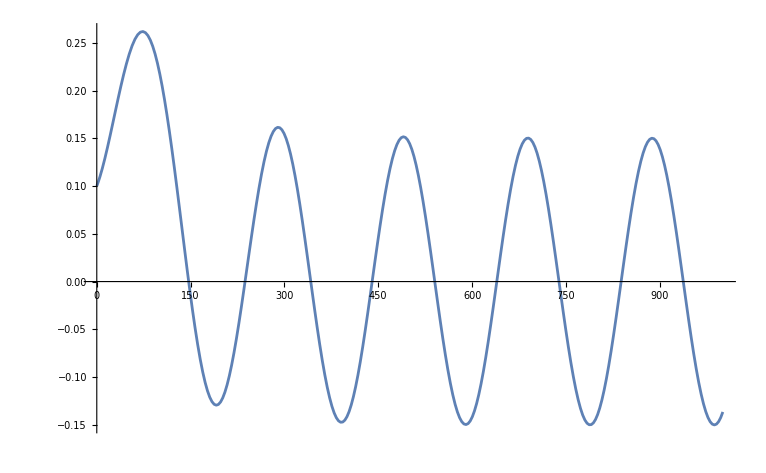

-Graphics3D-

```mathematica
data=NestWhileList[update,initial,#[[1]]<1000&];
Map[{#[[1]],#[[2,2]]}&,data]//ListLinePlot
lpp=Map[#[[2]]&,data]//ListLinePlot3D[#,BoxRatios->{1, 1, 1},PlotRange->{{-1,1},{-1,1},{-1,1}},PlotStyle->{Thin}]&
```

{S α-C β,R γ-C S δ,R S η-S λ}

(0 | -β | α
γ | -S δ | -C δ
S η | 0 | R η-λ)

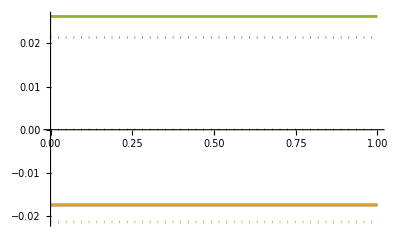

```mathematica
{
α S-β C,
γ R-δ S C, 
η R S - λ S
}
Solve[Map[#==0&,%],{R,C,S}];
Grad[%%,{R,C,S}];
%//MatrixForm
ReImPlot[Evaluate[%%/.%%%[[2]]/.{λ->0.01,η->0.04,γ->0.02,α->0.1,δ->0.03,β->0.05}//Eigenvalues],{δ,0,1}]
```